```mathematica
s1="[[0,1],[0,2],[1,2],[1,3],[2,3]]
[[0,1],[0,2],[1,2],[3,5],[4,5],[3,1],[4,2],[3,4],[4,3]]
[[0,1],[0,2],[1,2],[5,7],[6,7],[3,1],[4,2],[5,3],[6,4],[3,4],[4,3],[5,6],[6,5]]
[[0,1],[0,2],[1,2],[7,9],[8,9],[3,1],[4,2],[5,3],[6,4],[7,5],[8,6],[3,4],[4,3],[5,6],[6,5],[7,8],[8,7]]
[[0,1],[0,2],[1,2],[9,11],[10,11],[3,1],[4,2],[5,3],[6,4],[7,5],[8,6],[9,7],[10,8],[3,4],[4,3],[5,6],[6,5],[7,8],[8,7],[9,10],[10,9]]
[[0,1],[0,2],[1,2],[11,13],[12,13],[3,1],[4,2],[5,3],[6,4],[7,5],[8,6],[9,7],[10,8],[11,9],[12,10],[3,4],[4,3],[5,6],[6,5],[7,8],[8,7],[9,10],[10,9],[11,12],[12,11]]
[[0,1],[0,2],[1,2],[13,15],[14,15],[3,1],[4,2],[5,3],[6,4],[7,5],[8,6],[9,7],[10,8],[11,9],[12,10],[13,11],[14,12],[3,4],[4,3],[5,6],[6,5],[7,8],[8,7],[9,10],[10,9],[11,12],[12,11],[13,14],[14,13]]
[[0,1],[0,2],[1,2],[15,17],[16,17],[3,1],[4,2],[5,3],[6,4],[7,5],[8,6],[9,7],[10,8],[11,9],[12,10],[13,11],[14,12],[15,13],[16,14],[3,4],[4,3],[5,6],[6,5],[7,8],[8,7],[9,10],[10,9],[11,12],[12,11],[13,14],[14,13],[15,16],[16,15]]
[[0,1],[0,2],[1,2],[17,19],[18,19],[3,1],[4,2],[5,3],[6,4],[7,5],[8,6],[9,7],[10,8],[11,9],[12,10],[13,11],[14,12],[15,13],[16,14],[17,15],[18,16],[3,4],[4,3],[5,6],[6,5],[7,8],[8,7],[9,10],[10,9],[11,12],[12,11],[13,14],[14,13],[15,16],[16,15],[17,18],[18,17]]
[[0,1],[0,2],[1,2],[19,21],[20,21],[3,1],[4,2],[5,3],[6,4],[7,5],[8,6],[9,7],[10,8],[11,9],[12,10],[13,11],[14,12],[15,13],[16,14],[17,15],[18,16],[19,17],[20,18],[3,4],[4,3],[5,6],[6,5],[7,8],[8,7],[9,10],[10,9],[11,12],[12,11],[13,14],[14,13],[15,16],[16,15],[17,18],[18,17],[19,20],[20,19]]";
```

```mathematica
StringReplace[StringJoin["{",StringReplace[s1,{"\n"->",","["->"{","]"->"}"}],"}"],{"},{"->"!"}]
```

{{{0,1!0,2!1,2!1,3!2,3}!{0,1!0,2!1,2!3,5!4,5!3,1!4,2!3,4!4,3}!{0,1!0,2!1,2!5,7!6,7!3,1!4,2!5,3!6,4!3,4!4,3!5,6!6,5}!{0,1!0,2!1,2!7,9!8,9!3,1!4,2!5,3!6,4!7,5!8,6!3,4!4,3!5,6!6,5!7,8!8,7}!{0,1!0,2!1,2!9,11!10,11!3,1!4,2!5,3!6,4!7,5!8,6!9,7!10,8!3,4!4,3!5,6!6,5!7,8!8,7!9,10!10,9}!{0,1!0,2!1,2!11,13!12,13!3,1!4,2!5,3!6,4!7,5!8,6!9,7!10,8!11,9!12,10!3,4!4,3!5,6!6,5!7,8!8,7!9,10!10,9!11,12!12,11}!{0,1!0,2!1,2!13,15!14,15!3,1!4,2!5,3!6,4!7,5!8,6!9,7!10,8!11,9!12,10!13,11!14,12!3,4!4,3!5,6!6,5!7,8!8,7!9,10!10,9!11,12!12,11!13,14!14,13}!{0,1!0,2!1,2!15,17!16,17!3,1!4,2!5,3!6,4!7,5!8,6!9,7!10,8!11,9!12,10!13,11!14,12!15,13!16,14!3,4!4,3!5,6!6,5!7,8!8,7!9,10!10,9!11,12!12,11!13,14!14,13!15,16!16,15}!{0,1!0,2!1,2!17,19!18,19!3,1!4,2!5,3!6,4!7,5!8,6!9,7!10,8!11,9!12,10!13,11!14,12!15,13!16,14!17,15!18,16!3,4!4,3!5,6!6,5!7,8!8,7!9,10!10,9!11,12!12,11!13,14!14,13!15,16!16,15!17,18!18,17}!{0,1!0,2!1,2!19,21!20,21!3,1!4,2!5,3!6,4!7,5!8,6!9,7!10,8!11,9!12,10!13,11!14,12!15,13!16,14!17,15!18,16!19,17!20,18!3,4!4,3!5,6!6,5!7,8!8,7!9,10!10,9!11,12!12,11!13,14!14,13!15,16!16,15!17,18!18,17!19,20!20,19}}}

```mathematica
s4="[[0,1],[0,2],[0,3],[1,2],[2,3],[1,3]]
[[0,1],[0,2],[0,3],[0,4],[1,2],[2,3],[3,4],[1,4]]
[[0,1],[0,2],[0,3],[0,4],[0,5],[1,2],[2,3],[3,4],[4,5],[1,5]]
[[0,1],[0,2],[0,3],[0,4],[0,5],[0,6],[1,2],[2,3],[3,4],[4,5],[5,6],[1,6]]
[[0,1],[0,2],[0,3],[0,4],[0,5],[0,6],[0,7],[1,2],[2,3],[3,4],[4,5],[5,6],[6,7],[1,7]]
[[0,1],[0,2],[0,3],[0,4],[0,5],[0,6],[0,7],[0,8],[1,2],[2,3],[3,4],[4,5],[5,6],[6,7],[7,8],[1,8]]
[[0,1],[0,2],[0,3],[0,4],[0,5],[0,6],[0,7],[0,8],[0,9],[1,2],[2,3],[3,4],[4,5],[5,6],[6,7],[7,8],[8,9],[1,9]]
[[0,1],[0,2],[0,3],[0,4],[0,5],[0,6],[0,7],[0,8],[0,9],[0,10],[1,2],[2,3],[3,4],[4,5],[5,6],[6,7],[7,8],[8,9],[9,10],[1,10]]
[[0,1],[0,2],[0,3],[0,4],[0,5],[0,6],[0,7],[0,8],[0,9],[0,10],[0,11],[1,2],[2,3],[3,4],[4,5],[5,6],[6,7],[7,8],[8,9],[9,10],[10,11],[1,11]]
[[0,1],[0,2],[0,3],[0,4],[0,5],[0,6],[0,7],[0,8],[0,9],[0,10],[0,11],[0,12],[1,2],[2,3],[3,4],[4,5],[5,6],[6,7],[7,8],[8,9],[9,10],[10,11],[11,12],[1,12]]
[[0,1],[0,2],[0,3],[0,4],[0,5],[0,6],[0,7],[0,8],[0,9],[0,10],[0,11],[0,12],[0,13],[1,2],[2,3],[3,4],[4,5],[5,6],[6,7],[7,8],[8,9],[9,10],[10,11],[11,12],[12,13],[1,13]]
[[0,1],[0,2],[0,3],[0,4],[0,5],[0,6],[0,7],[0,8],[0,9],[0,10],[0,11],[0,12],[0,13],[0,14],[1,2],[2,3],[3,4],[4,5],[5,6],[6,7],[7,8],[8,9],[9,10],[10,11],[11,12],[12,13],[13,14],[1,14]]
[[0,1],[0,2],[0,3],[0,4],[0,5],[0,6],[0,7],[0,8],[0,9],[0,10],[0,11],[0,12],[0,13],[0,14],[0,15],[1,2],[2,3],[3,4],[4,5],[5,6],[6,7],[7,8],[8,9],[9,10],[10,11],[11,12],[12,13],[13,14],[14,15],[1,15]]
[[0,1],[0,2],[0,3],[0,4],[0,5],[0,6],[0,7],[0,8],[0,9],[0,10],[0,11],[0,12],[0,13],[0,14],[0,15],[0,16],[1,2],[2,3],[3,4],[4,5],[5,6],[6,7],[7,8],[8,9],[9,10],[10,11],[11,12],[12,13],[13,14],[14,15],[15,16],[1,16]]
[[0,1],[0,2],[0,3],[0,4],[0,5],[0,6],[0,7],[0,8],[0,9],[0,10],[0,11],[0,12],[0,13],[0,14],[0,15],[0,16],[0,17],[1,2],[2,3],[3,4],[4,5],[5,6],[6,7],[7,8],[8,9],[9,10],[10,11],[11,12],[12,13],[13,14],[14,15],[15,16],[16,17],[1,17]]
[[0,1],[0,2],[0,3],[0,4],[0,5],[0,6],[0,7],[0,8],[0,9],[0,10],[0,11],[0,12],[0,13],[0,14],[0,15],[0,16],[0,17],[0,18],[1,2],[2,3],[3,4],[4,5],[5,6],[6,7],[7,8],[8,9],[9,10],[10,11],[11,12],[12,13],[13,14],[14,15],[15,16],[16,17],[17,18],[1,18]]
[[0,1],[0,2],[0,3],[0,4],[0,5],[0,6],[0,7],[0,8],[0,9],[0,10],[0,11],[0,12],[0,13],[0,14],[0,15],[0,16],[0,17],[0,18],[0,19],[1,2],[2,3],[3,4],[4,5],[5,6],[6,7],[7,8],[8,9],[9,10],[10,11],[11,12],[12,13],[13,14],[14,15],[15,16],[16,17],[17,18],[18,19],[1,19]]";
```

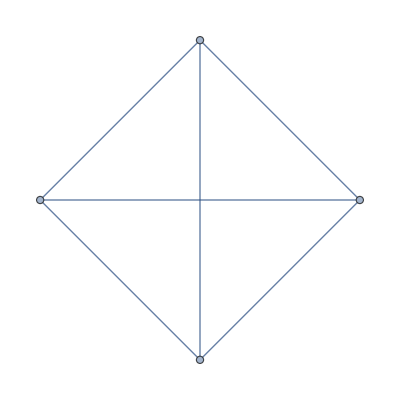
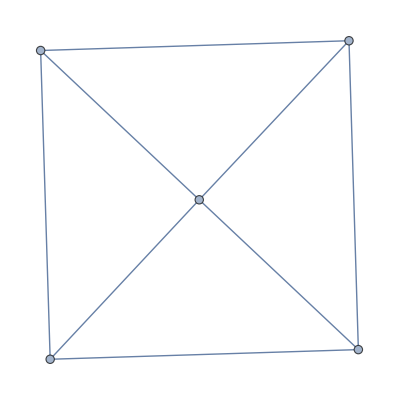
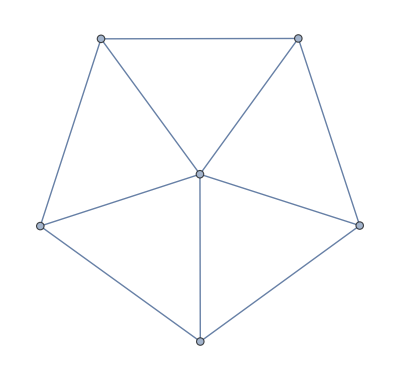
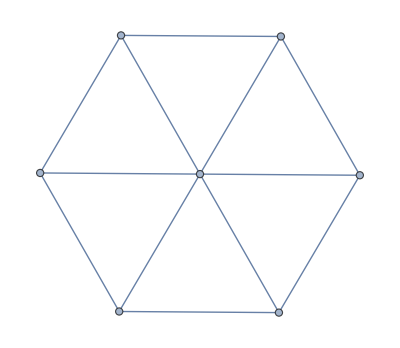
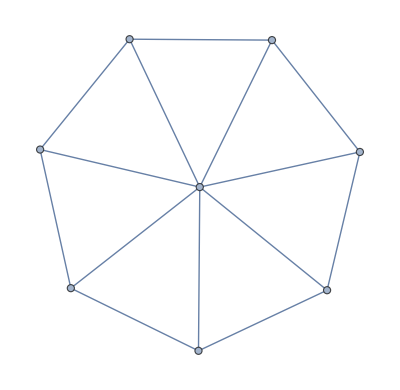
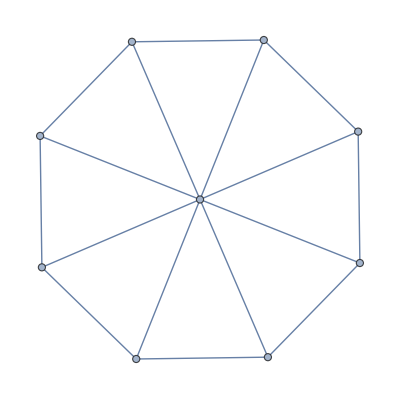
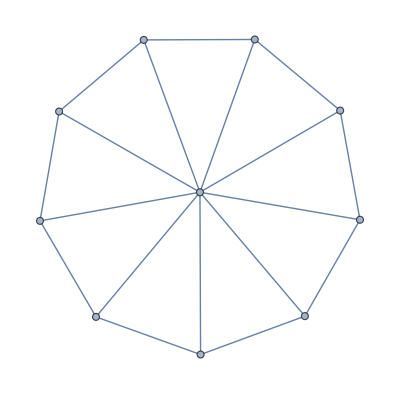
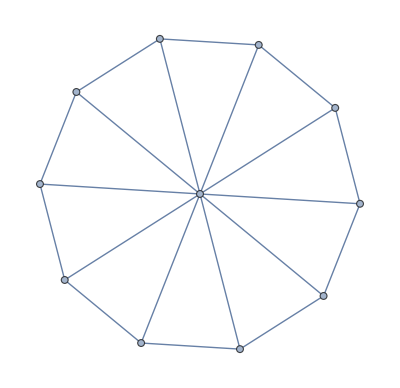

```mathematica
ws=Map[Graph,ToExpression[StringReplace[StringReplace[StringReplace[StringReplace[s4,{","->"<->"}],{"]<->["->","}],{"]\n["->","}],{"["->"{","]"->"}"}]]]
```

```mathematica
Table[IsomorphicGraphQ[ws[[i]],WheelGraph[i+3]],{i,1,Length[ws]}]
```

{True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True}

```mathematica
Map[numcy,ws]
```

{7,13,21,31,43,57,73,91,111,133,157,183,211,241,273,307,343}

```mathematica
Table[(n-1)(n-2)+1,{n,4,20}]
```

{7,13,21,31,43,57,73,91,111,133,157,183,211,241,273,307,343}

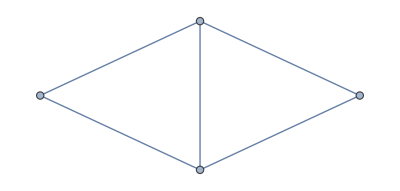
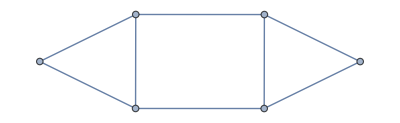
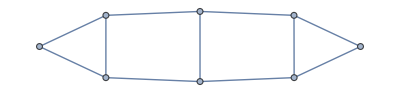
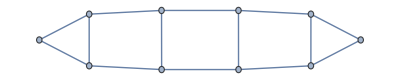
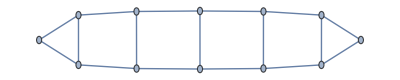
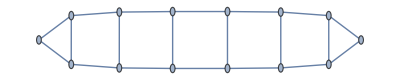
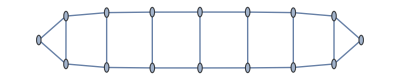
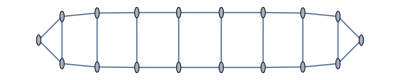

```mathematica
gs=Map[Graph,ToExpression[StringReplace[StringReplace[StringReplace[StringReplace[s3,{","->"<->"}],{"]<->["->","}],{"]\n["->","}],{"["->"{","]"->"}"}]]]
```

```mathematica
Length[gs]
```

20

```mathematica
Timing[numcy[WheelGraph[500]]]
```

{41.9307,248503}

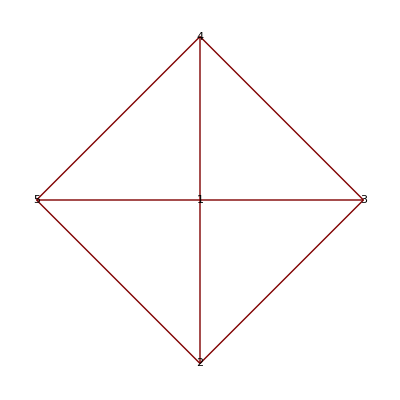

```mathematica
GraphPlot[WheelGraph[5],VertexLabeling->True]
```

```mathematica
1,2
1,3
1,4
1,5

2,3
3,4
4,5
5,2
```

```mathematica
Timing[ParallelTable[Timing[numcy[WheelGraph[i]]],{i,4,300}]]
```

{10.4421,{{0.001253,7},{0.000222,13},{0.000304,21},{0.000386,31},{0.000338,43},{0.000415,57},{0.000649,73},{0.000558,91},{0.000569,111},{0.00057,133},{0.000745,157},{0.000762,183},{0.000888,211},{0.001035,241},{0.001166,273},{0.00319,307},{0.001925,343},{0.001842,381},{0.001989,421},{0.002259,463},{0.002441,507},{0.003088,553},{0.003684,601},{0.003428,651},{0.004295,703},{0.00463,757},{0.005193,813},{0.00528,871},{0.005537,931},{0.007175,993},{0.008698,1057},{0.006966,1123},{0.007947,1191},{0.00961,1261},{0.00894,1333},{0.011091,1407},{0.010848,1483},{0.0111,1561},{0.012213,1641},{0.013577,1723},{0.014423,1807},{0.015264,1893},{0.015638,1981},{0.017093,2071},{0.017907,2163},{0.02077,2257},{0.021777,2353},{0.022304,2451},{0.02292,2551},{0.024071,2653},{0.02689,2757},{0.027274,2863},{0.028076,2971},{0.034367,3081},{0.036829,3193},{0.037203,3307},{0.040508,3423},{0.044935,3541},{0.0494,3661},{0.044564,3783},{0.044068,3907},{0.042854,4033},{0.04469,4161},{0.046102,4291},{0.058025,4423},{0.053609,4557},{0.061706,4693},{0.06646,4831},{0.067233,4971},{0.061339,5113},{0.063469,5257},{0.065137,5403},{0.071282,5551},{0.071447,5701},{0.073724,5853},{0.075493,6007},{0.080516,6163},{0.095584,6321},{0.090587,6481},{0.09855,6643},{0.092059,6807},{0.095564,6973},{0.09774,7141},{0.098651,7311},{0.103958,7483},{0.112783,7657},{0.110866,7833},{0.171163,8011},{0.121366,8191},{0.120702,8373},{0.14385,8557},{0.15202,8743},{0.141938,8931},{0.14568,9121},{0.144668,9313},{0.150116,9507},{0.156296,9703},{0.205649,9901},{0.172772,10101},{0.16908,10303},{0.17686,10507},{0.185271,10713},{0.193205,10921},{0.194266,11131},{0.191289,11343},{0.199937,11557},{0.209071,11773},{0.217465,11991},{0.264488,12211},{0.221596,12433},{0.229106,12657},{0.237795,12883},{0.246476,13111},{0.24321,13341},{0.250232,13573},{0.272792,13807},{0.267824,14043},{0.27936,14281},{0.28155,14521},{0.31059,14763},{0.293281,15007},{0.350462,15253},{0.314711,15501},{0.319636,15751},{0.325839,16003},{0.333355,16257},{0.361218,16513},{0.348868,16771},{0.366157,17031},{0.384336,17293},{0.419616,17557},{0.413884,17823},{0.476165,18091},{0.439565,18361},{0.422898,18633},{0.42315,18907},{0.429333,19183},{0.431271,19461},{0.451506,19741},{0.452319,20023},{0.485831,20307},{0.52927,20593},{0.527302,20881},{0.571663,21171},{0.516169,21463},{0.539797,21757},{0.555867,22053},{0.582147,22351},{0.586599,22651},{0.615211,22953},{0.60233,23257},{0.593728,23563},{0.659011,23871},{0.659104,24181},{0.733854,24493},{0.654196,24807},{0.684981,25123},{0.714851,25441},{0.713848,25761},{0.751809,26083},{0.773521,26407},{0.806305,26733},{0.815006,27061},{0.983511,27391},{0.852656,27723},{0.859151,28057},{0.891631,28393},{0.832193,28731},{0.858288,29071},{0.882988,29413},{0.889851,29757},{0.958594,30103},{0.966342,30451},{1.14401,30801},{1.00918,31153},{1.28137,31507},{1.08565,31863},{1.08416,32221},{1.14909,32581},{1.33401,32943},{1.07255,33307},{1.10884,33673},{1.12816,34041},{1.20467,34411},{1.32567,34783},{1.20581,35157},{1.48304,35533},{1.29325,35911},{1.31628,36291},{1.57597,36673},{1.39921,37057},{1.4228,37443},{1.39629,37831},{1.48547,38221},{1.5377,38613},{1.42641,39007},{1.61422,39403},{1.44959,39801},{1.79138,40201},{1.56129,40603},{1.84363,41007},{1.62551,41413},{1.67225,41821},{1.69799,42231},{1.78134,42643},{1.75821,43057},{1.82085,43473},{1.88665,43891},{1.86778,44311},{1.86148,44733},{2.12398,45157},{1.90236,45583},{2.15307,46011},{1.99369,46441},{2.02625,46873},{2.11743,47307},{2.07695,47743},{2.12944,48181},{2.18522,48621},{2.16112,49063},{2.23168,49507},{2.2804,49953},{2.3292,50401},{2.32097,50851},{2.40128,51303},{2.38741,51757},{2.39889,52213},{2.51262,52671},{2.54932,53131},{2.55256,53593},{2.60094,54057},{2.66616,54523},{2.71702,54991},{2.6443,55461},{2.71297,55933},{2.85526,56407},{2.94603,56883},{2.97565,57361},{2.93678,57841},{2.95293,58323},{3.03589,58807},{3.05669,59293},{3.04625,59781},{3.19936,60271},{3.14609,60763},{3.09861,61257},{3.27678,61753},{3.42538,62251},{3.40945,62751},{3.41096,63253},{3.43902,63757},{3.5143,64263},{3.45717,64771},{3.55995,65281},{3.66463,65793},{3.64008,66307},{3.67984,66823},{3.70896,67341},{4.00146,67861},{3.94712,68383},{3.92139,68907},{4.01623,69433},{4.02932,69961},{4.13752,70491},{4.00209,71023},{3.95113,71557},{3.81498,72093},{3.7982,72631},{3.82258,73171},{4.61878,73713},{4.59515,74257},{4.60062,74803},{4.60763,75351},{4.72223,75901},{4.67284,76453},{4.5137,77007},{4.36537,77563},{4.32975,78121},{4.25174,78681},{4.0976,79243},{4.05126,79807},{4.12212,80373},{4.29718,80941},{5.33609,81511},{5.35895,82083},{5.39138,82657},{4.92273,83233},{4.93731,83811},{4.91402,84391},{4.55666,84973},{4.62671,85557},{4.68204,86143},{4.79652,86731},{4.81807,87321},{4.87531,87913},{4.83174,88507},{4.92388,89103}}}

```mathematica
wr=Last[Out[18]];
```

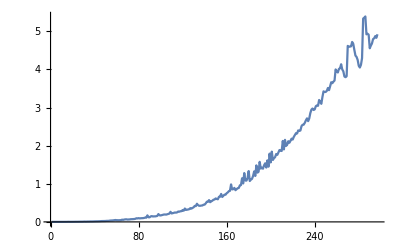

```mathematica
ListPlot[Map[First,wr],Joined->True]
```

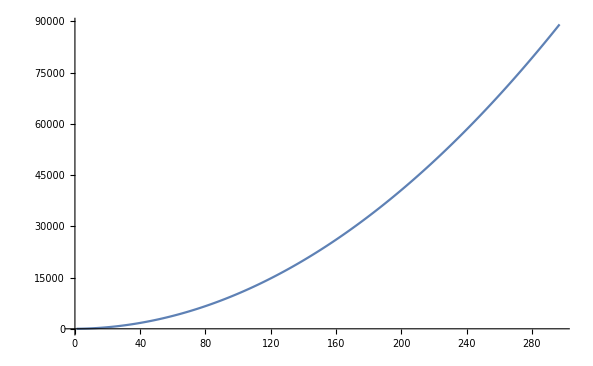

```mathematica
ListPlot[Map[Last[#]&,wr],Joined->True]
```

```mathematica
wrn=Map[Last[#]&,wr]
```

{7,13,21,31,43,57,73,91,111,133,157,183,211,241,273,307,343,381,421,463,507,553,601,651,703,757,813,871,931,993,1057,1123,1191,1261,1333,1407,1483,1561,1641,1723,1807,1893,1981,2071,2163,2257,2353,2451,2551,2653,2757,2863,2971,3081,3193,3307,3423,3541,3661,3783,3907,4033,4161,4291,4423,4557,4693,4831,4971,5113,5257,5403,5551,5701,5853,6007,6163,6321,6481,6643,6807,6973,7141,7311,7483,7657,7833,8011,8191,8373,8557,8743,8931,9121,9313,9507,9703,9901,10101,10303,10507,10713,10921,11131,11343,11557,11773,11991,12211,12433,12657,12883,13111,13341,13573,13807,14043,14281,14521,14763,15007,15253,15501,15751,16003,16257,16513,16771,17031,17293,17557,17823,18091,18361,18633,18907,19183,19461,19741,20023,20307,20593,20881,21171,21463,21757,22053,22351,22651,22953,23257,23563,23871,24181,24493,24807,25123,25441,25761,26083,26407,26733,27061,27391,27723,28057,28393,28731,29071,29413,29757,30103,30451,30801,31153,31507,31863,32221,32581,32943,33307,33673,34041,34411,34783,35157,35533,35911,36291,36673,37057,37443,37831,38221,38613,39007,39403,39801,40201,40603,41007,41413,41821,42231,42643,43057,43473,43891,44311,44733,45157,45583,46011,46441,46873,47307,47743,48181,48621,49063,49507,49953,50401,50851,51303,51757,52213,52671,53131,53593,54057,54523,54991,55461,55933,56407,56883,57361,57841,58323,58807,59293,59781,60271,60763,61257,61753,62251,62751,63253,63757,64263,64771,65281,65793,66307,66823,67341,67861,68383,68907,69433,69961,70491,71023,71557,72093,72631,73171,73713,74257,74803,75351,75901,76453,77007,77563,78121,78681,79243,79807,80373,80941,81511,82083,82657,83233,83811,84391,84973,85557,86143,86731,87321,87913,88507,89103}

```mathematica
enum[list_,start_]:=Table[{i+start-1,list[[i]]},{i,1,Length[list]}]
```

```mathematica
InterpolatingPolynomial[enum[wrn,4],n]
```

```mathematica
cyinwheel[n_]:=7+(-4+n) (1+n)
```

```mathematica
Reduce[(n-1)(n-2)+1==7+(-4+n) (1+n)]
```

True

```mathematica
"Antiprism"
```

```mathematica
show[class_]:=Map[GraphData,GraphData[class]]
```

```mathematica
Map[show,{"Apex","Apollonian","Archimedean"}]//Column
```

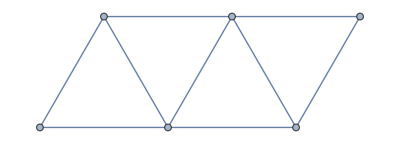

```mathematica
Timing[Table[numcy[GridGraph[{i,i}]],{i,2,6}]]
```

{24.8855,{1,13,213,9349,1222363}}

```mathematica
Table[numcy[GraphData[{"TriangularGrid",i}]],{i,1,5}]
```

{1,11,110,2402,128967}

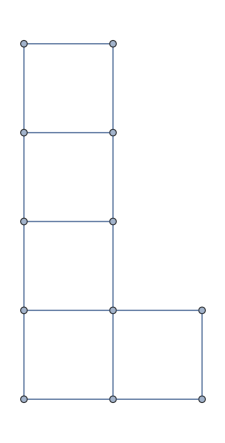

```mathematica
GraphData[{"Polyomino" ,{5,3}}]
```

```mathematica
GraphData["Classes"]
```

```mathematica
{"ArchimedeanDual","ArcTransitive","Arrangement","BananaTree","Barbell","Beineke","Bicolorable","Biconnected","Bicubic","Bipartite","BipartiteKneser","Bishop","BlackBishop","Book","Bouwer","Bridged","Bridgeless","Cactus","Cage","Caterpillar","Caveman","Cayley","Centipede","Chang","Chordal","ChromaticallyNonunique","ChromaticallyUnique","Circulant","Class1","Class2","ClawFree","CocktailParty","Complete","CompleteBipartite","CompletelyRegular","CompleteTree","CompleteTripartite","Cone","Conference","Connected","CriticalNonplanar","CrossedPrism","Crown","CubeConnectedCycle","Cubic","Cycle","Cyclic","Cyclotomic","DeterminedByResistance","DeterminedBySpectrum","Disconnected","DistanceRegular","DistanceTransitive","Doob","DutchWindmill","EdgeTransitive","Empty","Eulerian","Fan","Firecracker","Fiveleaper","FoldedCube","Forest","Fullerene","Fusene","Gear","GeneralizedPetersen","GeneralizedPolygon","GeneralizedPrism","Grid","Haar","Hadamard","Halin","HalvedCube","HamiltonConnected","HamiltonDecomposable","Hamiltonian","HamiltonLaceable","Hamming","Hanoi","Harary","Helm","HStarConnected","Hypercube","Hypohamiltonian","Hypotraceable","Identity","IGraph","Imperfect","Incidence","Integral","Johnson","Keller","KempeCounterexample","King","Kneser","Knight","Kuratowski","Ladder","LadderRung","Lattice","LCF","Line","Lobster","Local","LocallyPetersen","Lollipop","Matchstick","MaximallyNonhamiltonian","Metelsky","MoebiusLadder","MongolianTent","Moore","Mycielski","Noncayley","Noneulerian","Nonhamiltonian","Nonplanar","NoPerfectMatching","NotDeterminedByResistance","NotDeterminedBySpectrum","Octic","Odd","Paley","Pan","Path","Paulus","Perfect","PerfectMatching","PermutationStar","Planar","Platonic","Polyhedral","Polyiamond","Polyomino","Prism","Pseudoforest","Pseudotree","Quartic","Queen","Quintic","Regular","RegularPolychoron","Rook","SelfComplementary","SelfDual","Semisymmetric","Septic","Sextic","SierpinskiCarpet","SierpinskiSieve","Snark","Spider","SquareFree","StackedBook","Star","StronglyPerfect","StronglyRegular","Sun","Sunlet","Symmetric","Tadpole","Taylor","Tetrahedral","Toroidal","TorusGrid","Traceable","Tree","TriangleFree","Triangular","TriangularGrid","TriangularHoneycombAcuteKnight","TriangularHoneycombBishop","TriangularHoneycombKing","TriangularHoneycombObtuseKnight","TriangularHoneycombQueen","TriangularHoneycombRook","Triangulated","Tripod","Turan","TwoRegular","Unicyclic","UnitDistance","Untraceable","VertexTransitive","WeaklyPerfect","WeaklyRegular","Web","WellCovered","Wheel","WhiteBishop","Windmill","ZeroSymmetric","ZeroTwo"}
```

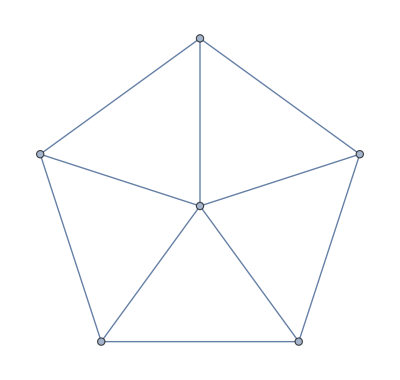

```mathematica
wg6=WheelGraph[6]
```

```mathematica
3+3+1
4+4+4+1
5+5+5+5+1
6+6+6+6+6+1
```

7

13

21

31

```mathematica
wrn
```

{7,13,21,31,43,57,73,91,111,133,157,183,211,241,273,307,343,381,421,463,507,553,601,651,703,757,813,871,931,993,1057,1123,1191,1261,1333,1407,1483,1561,1641,1723,1807,1893,1981,2071,2163,2257,2353,2451,2551,2653,2757,2863,2971,3081,3193,3307,3423,3541,3661,3783,3907,4033,4161,4291,4423,4557,4693,4831,4971,5113,5257,5403,5551,5701,5853,6007,6163,6321,6481,6643,6807,6973,7141,7311,7483,7657,7833,8011,8191,8373,8557,8743,8931,9121,9313,9507,9703,9901,10101,10303,10507,10713,10921,11131,11343,11557,11773,11991,12211,12433,12657,12883,13111,13341,13573,13807,14043,14281,14521,14763,15007,15253,15501,15751,16003,16257,16513,16771,17031,17293,17557,17823,18091,18361,18633,18907,19183,19461,19741,20023,20307,20593,20881,21171,21463,21757,22053,22351,22651,22953,23257,23563,23871,24181,24493,24807,25123,25441,25761,26083,26407,26733,27061,27391,27723,28057,28393,28731,29071,29413,29757,30103,30451,30801,31153,31507,31863,32221,32581,32943,33307,33673,34041,34411,34783,35157,35533,35911,36291,36673,37057,37443,37831,38221,38613,39007,39403,39801,40201,40603,41007,41413,41821,42231,42643,43057,43473,43891,44311,44733,45157,45583,46011,46441,46873,47307,47743,48181,48621,49063,49507,49953,50401,50851,51303,51757,52213,52671,53131,53593,54057,54523,54991,55461,55933,56407,56883,57361,57841,58323,58807,59293,59781,60271,60763,61257,61753,62251,62751,63253,63757,64263,64771,65281,65793,66307,66823,67341,67861,68383,68907,69433,69961,70491,71023,71557,72093,72631,73171,73713,74257,74803,75351,75901,76453,77007,77563,78121,78681,79243,79807,80373,80941,81511,82083,82657,83233,83811,84391,84973,85557,86143,86731,87321,87913,88507,89103}

```mathematica
cyinwheel[3]
```

3

```mathematica
ParallelTable[numcy[gs[[i]]],{i,1,20}]
```

```mathematica
Table[{i+1,Out[38][[i]]},{i,1,20}]
```

```mathematica
InterpolatingPolynomial[{{2,3},{3,6},{4,10},{5,15},{6,21},{7,28},{8,36},{9,45},{10,55},{11,66},{12,78},{13,91},{14,105},{15,120},{16,136},{17,153},{18,171},{19,190},{20,210},{21,231}},n]
```

```mathematica
Simplify[3+(3+1/2 (-3+n)) (-2+n)]
```

1/2 n (1+n)

```mathematica
InterpolatingPolynomial[{{1,3},{2,6},{3,10},{4,15},{5,21},{6,28},{7,36},{8,45},{9,55},{10,66},{11,78},{12,91},{13,105},{14,120},{15,136},{16,153},{17,171},{18,190},{19,210},{20,231}},n]
```

```mathematica
Simplify[3+(3+1/2 (-2+n)) (-1+n)]
```

1/2 (2+3 n+n^2)

```mathematica
1/2 (2+3 n+n^2)
```

```mathematica
InterpolatingPolynomial[{3,6,10,15,21,28,36,45,55,66,78,91,105,120,136,153,171,190,210,231},n]
```

```mathematica
Simplify[3+(3+1/2 (-2+n)) (-1+n)]
```

1/2 (2+3 n+n^2)

```mathematica
2+1
3+2+1
4+3+2+1
```

```mathematica
numcy[g_]:=Length[FindCycle[g,∞,All]]
```



```mathematica
CompleteGraph[3]
```

```mathematica
Table[numcy[CompleteGraph[n]],{n,3,12}]
```

$Aborted

```mathematica
Log2[556014]//N
```

19.0848

```mathematica
2^20
```

1048576

```mathematica
Map[PadLeft[#,25]&,{1,7,37,197,1172,8018,62814,556014}]
```

```mathematica
Table[InterpolatingPolynomial[Map[N[Log[#]/#^2]&,{1,7,37,197,1172,8018,62814,556014}],n]//Expand,{i,2,10}]//Column
```

-0.973486+2.13673 n-1.73058 n^2+0.711962 n^3-0.164962 n^4+0.0218335 n^5-0.0015418 n^6+0.0000450763 n^7
-0.973486+2.13673 n-1.73058 n^2+0.711962 n^3-0.164962 n^4+0.0218335 n^5-0.0015418 n^6+0.0000450763 n^7
-0.973486+2.13673 n-1.73058 n^2+0.711962 n^3-0.164962 n^4+0.0218335 n^5-0.0015418 n^6+0.0000450763 n^7
-0.973486+2.13673 n-1.73058 n^2+0.711962 n^3-0.164962 n^4+0.0218335 n^5-0.0015418 n^6+0.0000450763 n^7
-0.973486+2.13673 n-1.73058 n^2+0.711962 n^3-0.164962 n^4+0.0218335 n^5-0.0015418 n^6+0.0000450763 n^7
-0.973486+2.13673 n-1.73058 n^2+0.711962 n^3-0.164962 n^4+0.0218335 n^5-0.0015418 n^6+0.0000450763 n^7
-0.973486+2.13673 n-1.73058 n^2+0.711962 n^3-0.164962 n^4+0.0218335 n^5-0.0015418 n^6+0.0000450763 n^7
-0.973486+2.13673 n-1.73058 n^2+0.711962 n^3-0.164962 n^4+0.0218335 n^5-0.0015418 n^6+0.0000450763 n^7
-0.973486+2.13673 n-1.73058 n^2+0.711962 n^3-0.164962 n^4+0.0218335 n^5-0.0015418 n^6+0.0000450763 n^7

```mathematica
cgc[n_]:=ParallelTable[Length[FindCycle[CompleteGraph[n],{l},All]],{l,3,n+1}]
```

```mathematica
cgc[3]
```

{1,0}

```mathematica
cgc[4]
```

{4,3,0}

```mathematica
cgc[5]
```

{10,15,12,0}

```mathematica
cgc[6]
```

{20,45,72,60,0}

```mathematica
cgc[7]
```

{35,105,252,420,360,0}

```mathematica
cgc[8]
```

{56,210,672,1680,2880,2520,0}

```mathematica
cgc[9]
```

{84,378,1512,5040,12960,22680,20160,0}

```mathematica
cgc[10]
```

{120,630,3024,12600,43200,113400,201600,181440,0}

```mathematica
cgc[11]
```

{165,990,5544,27720,118800,415800,1108800,1995840,1814400,0}

```mathematica
cgc[12]
```

```mathematica
Table[numcy[CompleteGraph[n]],{n,2,11}]
```

{0,1,7,37,197,1172,8018,62814,556014,5488059}

```mathematica
FindCycle[CompleteGraph[4],{4},All]
```

{{1<->4,4<->3,3<->2,2<->1},{1<->2,2<->4,4<->3,3<->1},{1<->4,4<->2,2<->3,3<->1}}

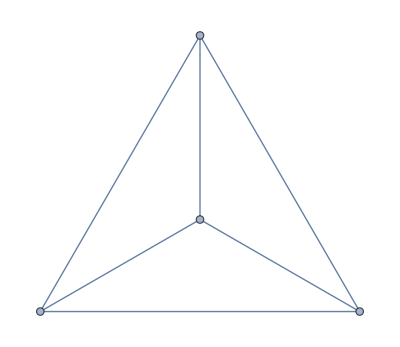

```mathematica
CompleteGraph[4]
```

```mathematica
"'k' is the size of the cycles where k==0 -> cycle size 3";
"'n' is CompleteGraph[n+2]";
"The formula is divided by 'k' because with cycles of size k, there are k orientation of each cycle."
"cycles size k require three choices: n possibilities, n-1, n-2 etc."
```

```mathematica
Sum[Product[(i-k+n)/2k,{i,1,k}],{k,3,n}]
```

```mathematica
Table[∑_(k=3)^n ((∏_(i=1)^k (i-k+n))/(2k)),{n,3,11}]
```

{1,7,37,197,1172,8018,62814,556014,5488059}

```mathematica
Table[numcy[CompleteGraph[n]],{n,3,11}]
```

{1,7,37,197,1172,8018,62814,556014,5488059}

```mathematica
FullSimplify[((n-2)+i-(k-3))]
```

```mathematica
∑_(k=3)^n ((∏_(i=1)^k (i-k+n))/(2k))
```

1/2 Gamma[1+n] (1/2 (-1/Gamma[n]-n/Gamma[n])+DifferenceRoot[Function[{y,n},{n (-n+n) y[n]+(-1-n+n^2-n n) y[1+n]+(1+n) y[2+n]==0,y[1]==0,y[2]==1/Gamma[n]}]][1+n])

```mathematica
FullSimplify[1/2 Gamma[1+n] (1/2 (-1/Gamma[n]-n/Gamma[n])+a),{Element[n,Integers],n≥0}]
```

-1/4 n (1+n)+(a n!)/2

```mathematica
FullSimplify[1/4 (-1/Gamma[n]-n/Gamma[n]) Gamma[1+n],{Element[n,Integers],n≥0}]
```

-1/4 n (1+n)

```mathematica
∏_(i=1)^k (i-k+n)
```

Pochhammer[1-k+n,k]

```mathematica
FullSimplify[(∑_(k=3)^n (Pochhammer[1-k+n,k]/(Gamma[1+n]k)))-1/2 (-1/Gamma[n]-n/Gamma[n]),{Element[n,Integers],n≥0}]
```

DifferenceRoot[Function[{y,n},{n (-n+n) y[n]+(-1+n^2-n (1+n)) y[1+n]+(1+n) y[2+n]==0,y[1]==0,y[2]==1/Gamma[n]}]][1+n]

```mathematica
∑_(k=3)^n ((∏_(i=1)^k (i-k+n))/(Gamma[1+n]k))==1/2 Gamma[1+n] (1/2 (-1/Gamma[n]-n/Gamma[n])+DifferenceRoot[Function[{y,n},{n (-n+n) y[n]+(-1-n+n^2-n n) y[1+n]+(1+n) y[2+n]==0,y[1]==0,y[2]==1/Gamma[n]}]][1+n])
```

```mathematica
dr=Monitor[Table[DifferenceRoot[Function[{y,n},{n (-n+n) y[n]+(-1-n+n^2-n n) y[1+n]+(1+n) y[2+n]==0,y[1]==0,y[2]==1/Gamma[n]}]][1+n],{n,1,1000}],n];
```

```mathematica
drf[n_]=DifferenceRoot[Function[{y,n},{n (-n+n) y[n]+(-1-n+n^2-n n) y[1+n]+(1+n) y[2+n]==0,y[1]==0,y[2]==1/Gamma[n]}]][1+n];
```

```mathematica
N[drf[1000]]
```

0.00272101

```mathematica
N[drf[2000]]
```

0.00135982

```mathematica
N[drf[4000]]
```

0.00067974

```mathematica
N[drf[8000]]
```

0.000339828

```mathematica
N[drf[16000]]
```

$Aborted

```mathematica
N[Last[dr]]
```

0.00272101

```mathematica
f=DifferenceRoot[Function[{y,n},{n (-n+n) y[n]+(-1-n+n^2-n n) y[1+n]+(1+n) y[2+n]==0,y[1]==0,y[2]==1/Gamma[n]}]][1+n];
```

```mathematica
oΔe=First[Head[f]][y,n]
```

```mathematica
RSolve[{(-1-n) y[1+n]+(1+n) y[2+n]==0,y[1]==0,y[2]==1/Gamma[n]},y,n]
```

RSolve::bvnul: For some branches of the general solution, the given boundary conditions lead to an empty solution.

{}

```mathematica
Reduce[{DifferenceRoot[Function[{y,n},{n (-n+n) y[n]+(-1-n+n^2-n n) y[1+n]+(1+n) y[2+n]==0,y[1]==0,y[2]==1/Gamma[n]}]][1+n]>DifferenceRoot[Function[{y,n},{n (-n+n) y[n]+(-1-n+n^2-n n) y[1+n]+(1+n) y[2+n]==0,y[1]==0,y[2]==1/Gamma[n]}]][5+n],n>0},Integers]
```

Reduce::nsmet: This system cannot be solved with the methods available to Reduce.

Reduce[{DifferenceRoot[Function[{y,n},{n (-n+n) y[n]+(-1-n+n^2-n n) y[1+n]+(1+n) y[2+n]==0,y[1]==0,y[2]==1/Gamma[n]}]][1+n]>DifferenceRoot[Function[{y,n},{n (-n+n) y[n]+(-1-n+n^2-n n) y[1+n]+(1+n) y[2+n]==0,y[1]==0,y[2]==1/Gamma[n]}]][5+n],n>0},Integers]

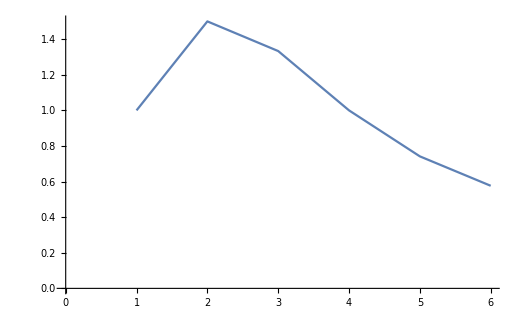

```mathematica
ListPlot[Table[(DifferenceRoot[Function[{y,n},{n (-n+n) y[n]+(-1-n+n^2-n n) y[1+n]+(1+n) y[2+n]==0,y[1]==0,y[2]==1/Gamma[n]}]][1+n]),{n,1,6}],Joined->True]
```

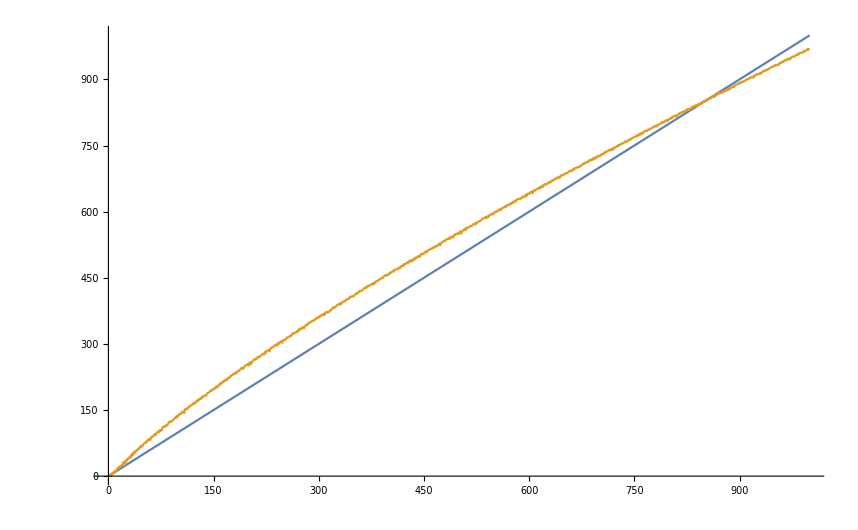

```mathematica
ListPlot[{Range[1,1000],Map[Log2[Denominator[#]]*#^(1/ⅇ)&,dr]},Joined->True]
```

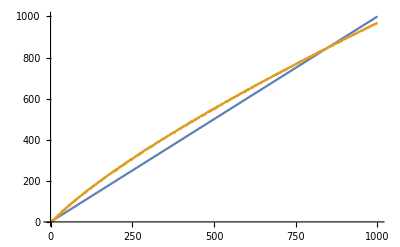

```mathematica
ListPlot[{Range[1,1000],Map[Log2[Numerator[#]]*#^(1/ⅇ)&,dr]},Joined->True]
```

```mathematica
FullSimplify[DifferenceRoot[Function[{y,n},{n (-n+n) y[n]+(-1-n+n^2-n n) y[1+n]+(1+n) y[2+n]==0,y[1]==0,y[2]==1/Gamma[n]}]][1+n],{Element[n,Integers],n≥0}]
```

DifferenceRoot[Function[{y,n},{n (-n+n) y[n]+(-1+n^2-n (1+n)) y[1+n]+(1+n) y[2+n]==0,y[1]==0,y[2]==1/Gamma[n]}]][1+n]

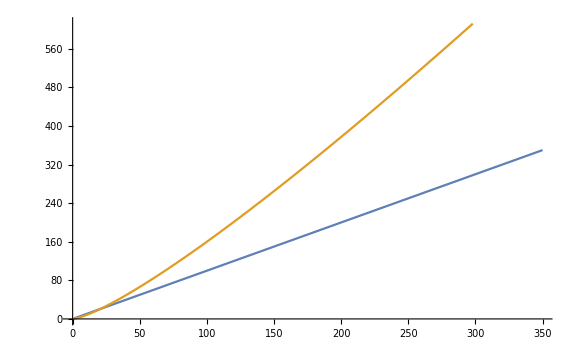

```mathematica
ListPlot[{Range[350],Table[Log10[∑_(k=3)^n ((∏_(i=1)^k (i-k+n))/(2k))],{n,3,300}]},Joined->True]
```

```mathematica
Table[∑_(k=0)^n (∏_(i=-k)^2 (n+i))/(2(k+3)),{n,1,10}]
```

{1,7,37,197,1172,8018,62814,556014,5488059,59740609}

```mathematica
Map[CoefficientList[Expand[#],n]&,Table[∏_(i=1)^k (i-k+n),{k,3,15}]]//Column
```

{0,2,-3,1}
{0,-6,11,-6,1}
{0,24,-50,35,-10,1}
{0,-120,274,-225,85,-15,1}
{0,720,-1764,1624,-735,175,-21,1}
{0,-5040,13068,-13132,6769,-1960,322,-28,1}
{0,40320,-109584,118124,-67284,22449,-4536,546,-36,1}
{0,-362880,1026576,-1172700,723680,-269325,63273,-9450,870,-45,1}
{0,3628800,-10628640,12753576,-8409500,3416930,-902055,157773,-18150,1320,-55,1}
{0,-39916800,120543840,-150917976,105258076,-45995730,13339535,-2637558,357423,-32670,1925,-66,1}
{0,479001600,-1486442880,1931559552,-1414014888,657206836,-206070150,44990231,-6926634,749463,-55770,2717,-78,1}
{0,-6227020800,19802759040,-26596717056,20313753096,-9957703756,3336118786,-790943153,135036473,-16669653,1474473,-91091,3731,-91,1}
{0,87178291200,-283465647360,392156797824,-310989260400,159721605680,-56663366760,14409322928,-2681453775,368411615,-37312275,2749747,-143325,5005,-105,1}

```mathematica
FullSimplify[∑_(k=3)^n (∏_(i=1)^k (i-k+n))/k,{Element[n,Integers],n≥0}]
```

-1/2 n (1+n)+n! DifferenceRoot[Function[{y,n},{n (-n+n) y[n]+(-1+n^2-n (1+n)) y[1+n]+(1+n) y[2+n]==0,y[1]==0,y[2]==1/Gamma[n]}]][1+n]

```mathematica
FullSimplify[∑_(k=3)^n n^k/k,{Element[n,Integers],n≥0}]
```

```mathematica
FullSimplify[-1/2 n (2+n)+n^(1+n)ⅇ^-n-Log[1-n]]
```

ⅇ^-n n^(1+n)-1/2 n (2+n)-Log[1-n]

```mathematica
Solve[-Log[-y]==x,y]
```

{{y→ConditionalExpression[-ⅇ^-x,-π≤Im[x]<π]}}

```mathematica
Expand[N[InterpolatingPolynomial[Table[-Log[-LerchPhi[n,1,1+n]],{n,12,25}],n]]]
```

```mathematica
FullSimplify[∏_(i=0)^(2+(k-3)) ((n-2)+i-(k-3))]
```

Gamma[1+n]/Gamma[1-k+n]

```mathematica
Table[∏_(i=0)^(2+(k-3)) ((n-2)+i-(k-3)),{k,3,10}]//Column
```

(-2+n) (-1+n) n
(-3+n) (-2+n) (-1+n) n
(-4+n) (-3+n) (-2+n) (-1+n) n
(-5+n) (-4+n) (-3+n) (-2+n) (-1+n) n
(-6+n) (-5+n) (-4+n) (-3+n) (-2+n) (-1+n) n
(-7+n) (-6+n) (-5+n) (-4+n) (-3+n) (-2+n) (-1+n) n
(-8+n) (-7+n) (-6+n) (-5+n) (-4+n) (-3+n) (-2+n) (-1+n) n
(-9+n) (-8+n) (-7+n) (-6+n) (-5+n) (-4+n) (-3+n) (-2+n) (-1+n) n

```mathematica
FullSimplify[(∏_(i=0)^(2+k) (n+i-k))/(2(k+3))]
```

Gamma[3+n]/(2 (3+k) Gamma[-k+n])

```mathematica
(∏_(i=0)^(2+k) (n+i-k))/(2(k+3))==(∏_(i=-k)^2 (n+i))/(2(k+3))
```

```mathematica
FullSimplify[(∏_(i=-k)^2 (n+i))/(2(k+3)),{Element[n,Integers],n≥0,Element[k,Integers],k≥0}]
```

```mathematica
FullSimplify[Pochhammer[-k+n,3+k]/(6+2 k)]
```

Pochhammer[-k+n,3+k]/(6+2 k)

```mathematica
FullSimplify[∑_(k=0)^n (∏_(i=-k)^2 (n+i))/(2(k+3)),Element[n,Integers]&&n≥0]
```

```mathematica
Table[∑_(k=0)^n (∏_(i=-k)^2 (n+i))/(2(k+3)),{n,0,10}]
```

{0,1,7,37,197,1172,8018,62814,556014,5488059,59740609}

```mathematica
Table[Table[(∏_(i=-k)^2 (n+i))/(2(k+3)),{k,0,10}],{n,0,10}]//Column
```

{0,0,0,0,0,0,0,0,0,0,0}
{1,0,0,0,0,0,0,0,0,0,0}
{4,3,0,0,0,0,0,0,0,0,0}
{10,15,12,0,0,0,0,0,0,0,0}
{20,45,72,60,0,0,0,0,0,0,0}
{35,105,252,420,360,0,0,0,0,0,0}
{56,210,672,1680,2880,2520,0,0,0,0,0}
{84,378,1512,5040,12960,22680,20160,0,0,0,0}
{120,630,3024,12600,43200,113400,201600,181440,0,0,0}
{165,990,5544,27720,118800,415800,1108800,1995840,1814400,0,0}
{220,1485,9504,55440,285120,1247400,4435200,11975040,21772800,19958400,0}

```mathematica
Expand[InterpolatingPolynomial[{0,0,0,0,360,2880,12960,43200,118800},n]]
```

```mathematica
Factor[(24 n)/7-2 n^2-4 n^3+(5 n^4)/2+n^5/2-n^6/2+n^7/14]
```

1/14 (-4+n) (-3+n) (-2+n) (-1+n) n (1+n) (2+n)

```mathematica
Expand[InterpolatingPolynomial[{0,0,0,60,420,1680,5040,12600,27720},n]]
```

```mathematica
Factor[-n+n^2/3+(5 n^3)/4-(5 n^4)/12-n^5/4+n^6/12]
```

1/12 (-3+n) (-2+n) (-1+n) n (1+n) (2+n)

```mathematica
Expand[InterpolatingPolynomial[{0,0,12,72,252,672,1512,3024,5544},n]]
```

```mathematica
Factor[(2 n)/5-n^3/2+n^5/10]
```

1/10 (-2+n) (-1+n) n (1+n) (2+n)

```mathematica
Expand[InterpolatingPolynomial[{0,3,15,45,105,210,378,630,990},n]]
```

-n/4-n^2/8+n^3/4+n^4/8

```mathematica
Factor[-n/4-n^2/8+n^3/4+n^4/8]
```

1/8 (-1+n) n (1+n) (2+n)

```mathematica
Expand[InterpolatingPolynomial[{{2,0},{3,1},{4,4},{5,10},{6,20},{7,35},{8,56},{9,84},{10,120},{11,165}},n]]==Expand[Binomial[n,3]]
```

True

```mathematica
Factor[Expand[Binomial[n,3]]]
```

1/6 (-2+n) (-1+n) n

```mathematica
ArrayPlot[Map[PadLeft[IntegerDigits[#,2],26]&,{1,0,1,0,7,0,7,0,37,0,63,0,197,0,255,0,1172,0,2047,0,8018,0,8191,0,62814,0,65535,0,556014,0,1048575}]]
```

-Graphics-

```mathematica
numcy[CompleteGraph[3]]
```

1

```mathematica
s2="[[0,1],[0,2],[1,2],[1,3],[2,3]]
[[0,1],[0,2],[1,2],[3,5],[4,5],[3,1],[4,2],[3,4]]
[[0,1],[0,2],[1,2],[5,7],[6,7],[3,1],[4,2],[5,3],[6,4],[3,4],[5,6]]
[[0,1],[0,2],[1,2],[7,9],[8,9],[3,1],[4,2],[5,3],[6,4],[7,5],[8,6],[3,4],[5,6],[7,8]]
[[0,1],[0,2],[1,2],[9,11],[10,11],[3,1],[4,2],[5,3],[6,4],[7,5],[8,6],[9,7],[10,8],[3,4],[5,6],[7,8],[9,10]]
[[0,1],[0,2],[1,2],[11,13],[12,13],[3,1],[4,2],[5,3],[6,4],[7,5],[8,6],[9,7],[10,8],[11,9],[12,10],[3,4],[5,6],[7,8],[9,10],[11,12]]
[[0,1],[0,2],[1,2],[13,15],[14,15],[3,1],[4,2],[5,3],[6,4],[7,5],[8,6],[9,7],[10,8],[11,9],[12,10],[13,11],[14,12],[3,4],[5,6],[7,8],[9,10],[11,12],[13,14]]
[[0,1],[0,2],[1,2],[15,17],[16,17],[3,1],[4,2],[5,3],[6,4],[7,5],[8,6],[9,7],[10,8],[11,9],[12,10],[13,11],[14,12],[15,13],[16,14],[3,4],[5,6],[7,8],[9,10],[11,12],[13,14],[15,16]]
[[0,1],[0,2],[1,2],[17,19],[18,19],[3,1],[4,2],[5,3],[6,4],[7,5],[8,6],[9,7],[10,8],[11,9],[12,10],[13,11],[14,12],[15,13],[16,14],[17,15],[18,16],[3,4],[5,6],[7,8],[9,10],[11,12],[13,14],[15,16],[17,18]]
[[0,1],[0,2],[1,2],[19,21],[20,21],[3,1],[4,2],[5,3],[6,4],[7,5],[8,6],[9,7],[10,8],[11,9],[12,10],[13,11],[14,12],[15,13],[16,14],[17,15],[18,16],[19,17],[20,18],[3,4],[5,6],[7,8],[9,10],[11,12],[13,14],[15,16],[17,18],[19,20]]";
```

```mathematica
s3="[[0,1],[0,2],[1,2],[1,3],[2,3]]
[[0,1],[0,2],[1,2],[3,5],[4,5],[3,1],[4,2],[3,4]]
[[0,1],[0,2],[1,2],[5,7],[6,7],[3,1],[4,2],[5,3],[6,4],[3,4],[5,6]]
[[0,1],[0,2],[1,2],[7,9],[8,9],[3,1],[4,2],[5,3],[6,4],[7,5],[8,6],[3,4],[5,6],[7,8]]
[[0,1],[0,2],[1,2],[9,11],[10,11],[3,1],[4,2],[5,3],[6,4],[7,5],[8,6],[9,7],[10,8],[3,4],[5,6],[7,8],[9,10]]
[[0,1],[0,2],[1,2],[11,13],[12,13],[3,1],[4,2],[5,3],[6,4],[7,5],[8,6],[9,7],[10,8],[11,9],[12,10],[3,4],[5,6],[7,8],[9,10],[11,12]]
[[0,1],[0,2],[1,2],[13,15],[14,15],[3,1],[4,2],[5,3],[6,4],[7,5],[8,6],[9,7],[10,8],[11,9],[12,10],[13,11],[14,12],[3,4],[5,6],[7,8],[9,10],[11,12],[13,14]]
[[0,1],[0,2],[1,2],[15,17],[16,17],[3,1],[4,2],[5,3],[6,4],[7,5],[8,6],[9,7],[10,8],[11,9],[12,10],[13,11],[14,12],[15,13],[16,14],[3,4],[5,6],[7,8],[9,10],[11,12],[13,14],[15,16]]
[[0,1],[0,2],[1,2],[17,19],[18,19],[3,1],[4,2],[5,3],[6,4],[7,5],[8,6],[9,7],[10,8],[11,9],[12,10],[13,11],[14,12],[15,13],[16,14],[17,15],[18,16],[3,4],[5,6],[7,8],[9,10],[11,12],[13,14],[15,16],[17,18]]
[[0,1],[0,2],[1,2],[19,21],[20,21],[3,1],[4,2],[5,3],[6,4],[7,5],[8,6],[9,7],[10,8],[11,9],[12,10],[13,11],[14,12],[15,13],[16,14],[17,15],[18,16],[19,17],[20,18],[3,4],[5,6],[7,8],[9,10],[11,12],[13,14],[15,16],[17,18],[19,20]]
[[0,1],[0,2],[1,2],[21,23],[22,23],[3,1],[4,2],[5,3],[6,4],[7,5],[8,6],[9,7],[10,8],[11,9],[12,10],[13,11],[14,12],[15,13],[16,14],[17,15],[18,16],[19,17],[20,18],[21,19],[22,20],[3,4],[5,6],[7,8],[9,10],[11,12],[13,14],[15,16],[17,18],[19,20],[21,22]]
[[0,1],[0,2],[1,2],[23,25],[24,25],[3,1],[4,2],[5,3],[6,4],[7,5],[8,6],[9,7],[10,8],[11,9],[12,10],[13,11],[14,12],[15,13],[16,14],[17,15],[18,16],[19,17],[20,18],[21,19],[22,20],[23,21],[24,22],[3,4],[5,6],[7,8],[9,10],[11,12],[13,14],[15,16],[17,18],[19,20],[21,22],[23,24]]
[[0,1],[0,2],[1,2],[25,27],[26,27],[3,1],[4,2],[5,3],[6,4],[7,5],[8,6],[9,7],[10,8],[11,9],[12,10],[13,11],[14,12],[15,13],[16,14],[17,15],[18,16],[19,17],[20,18],[21,19],[22,20],[23,21],[24,22],[25,23],[26,24],[3,4],[5,6],[7,8],[9,10],[11,12],[13,14],[15,16],[17,18],[19,20],[21,22],[23,24],[25,26]]
[[0,1],[0,2],[1,2],[27,29],[28,29],[3,1],[4,2],[5,3],[6,4],[7,5],[8,6],[9,7],[10,8],[11,9],[12,10],[13,11],[14,12],[15,13],[16,14],[17,15],[18,16],[19,17],[20,18],[21,19],[22,20],[23,21],[24,22],[25,23],[26,24],[27,25],[28,26],[3,4],[5,6],[7,8],[9,10],[11,12],[13,14],[15,16],[17,18],[19,20],[21,22],[23,24],[25,26],[27,28]]
[[0,1],[0,2],[1,2],[29,31],[30,31],[3,1],[4,2],[5,3],[6,4],[7,5],[8,6],[9,7],[10,8],[11,9],[12,10],[13,11],[14,12],[15,13],[16,14],[17,15],[18,16],[19,17],[20,18],[21,19],[22,20],[23,21],[24,22],[25,23],[26,24],[27,25],[28,26],[29,27],[30,28],[3,4],[5,6],[7,8],[9,10],[11,12],[13,14],[15,16],[17,18],[19,20],[21,22],[23,24],[25,26],[27,28],[29,30]]
[[0,1],[0,2],[1,2],[31,33],[32,33],[3,1],[4,2],[5,3],[6,4],[7,5],[8,6],[9,7],[10,8],[11,9],[12,10],[13,11],[14,12],[15,13],[16,14],[17,15],[18,16],[19,17],[20,18],[21,19],[22,20],[23,21],[24,22],[25,23],[26,24],[27,25],[28,26],[29,27],[30,28],[31,29],[32,30],[3,4],[5,6],[7,8],[9,10],[11,12],[13,14],[15,16],[17,18],[19,20],[21,22],[23,24],[25,26],[27,28],[29,30],[31,32]]
[[0,1],[0,2],[1,2],[33,35],[34,35],[3,1],[4,2],[5,3],[6,4],[7,5],[8,6],[9,7],[10,8],[11,9],[12,10],[13,11],[14,12],[15,13],[16,14],[17,15],[18,16],[19,17],[20,18],[21,19],[22,20],[23,21],[24,22],[25,23],[26,24],[27,25],[28,26],[29,27],[30,28],[31,29],[32,30],[33,31],[34,32],[3,4],[5,6],[7,8],[9,10],[11,12],[13,14],[15,16],[17,18],[19,20],[21,22],[23,24],[25,26],[27,28],[29,30],[31,32],[33,34]]
[[0,1],[0,2],[1,2],[35,37],[36,37],[3,1],[4,2],[5,3],[6,4],[7,5],[8,6],[9,7],[10,8],[11,9],[12,10],[13,11],[14,12],[15,13],[16,14],[17,15],[18,16],[19,17],[20,18],[21,19],[22,20],[23,21],[24,22],[25,23],[26,24],[27,25],[28,26],[29,27],[30,28],[31,29],[32,30],[33,31],[34,32],[35,33],[36,34],[3,4],[5,6],[7,8],[9,10],[11,12],[13,14],[15,16],[17,18],[19,20],[21,22],[23,24],[25,26],[27,28],[29,30],[31,32],[33,34],[35,36]]
[[0,1],[0,2],[1,2],[37,39],[38,39],[3,1],[4,2],[5,3],[6,4],[7,5],[8,6],[9,7],[10,8],[11,9],[12,10],[13,11],[14,12],[15,13],[16,14],[17,15],[18,16],[19,17],[20,18],[21,19],[22,20],[23,21],[24,22],[25,23],[26,24],[27,25],[28,26],[29,27],[30,28],[31,29],[32,30],[33,31],[34,32],[35,33],[36,34],[37,35],[38,36],[3,4],[5,6],[7,8],[9,10],[11,12],[13,14],[15,16],[17,18],[19,20],[21,22],[23,24],[25,26],[27,28],[29,30],[31,32],[33,34],[35,36],[37,38]]
[[0,1],[0,2],[1,2],[39,41],[40,41],[3,1],[4,2],[5,3],[6,4],[7,5],[8,6],[9,7],[10,8],[11,9],[12,10],[13,11],[14,12],[15,13],[16,14],[17,15],[18,16],[19,17],[20,18],[21,19],[22,20],[23,21],[24,22],[25,23],[26,24],[27,25],[28,26],[29,27],[30,28],[31,29],[32,30],[33,31],[34,32],[35,33],[36,34],[37,35],[38,36],[39,37],[40,38],[3,4],[5,6],[7,8],[9,10],[11,12],[13,14],[15,16],[17,18],[19,20],[21,22],[23,24],[25,26],[27,28],[29,30],[31,32],[33,34],[35,36],[37,38],[39,40]]";
```